```mathematica
m0=5.5;          (*MeV*) 
T0=270;          (*MeV*) 
a0 = 6.75;
a1=-1.95;
a2 =2.625;
a3 =-7.44;
b3 =0.75;
b4=7.5;
 =651 ;       (*MeV*)
G = 10.08*10^-6;       (*MeV^-2*)
Nf=2;
e[p_,z_] :=√(p^2+(m0-G*z)^2);
b2[T_]:=a0 + a1(T0/T)+a2(T0/T)^2+a3(T0/T)^3;
U[x_,T_] := ((-b2[T])/2*x^2-b3/3*(x^3)+b4/4*x^4)*T^4;
 [x_,z_,T_]:=U[x,T]+z^2/2*G-2*Nf*T*NIntegrate[p^2/(2*π^2)*(Log[1+3*x*ⅇ^(-e[p,z]/T)+3*x*ⅇ^(-2*e[p,z]/T)+ⅇ^(-3*e[p,z]/T)]+Log[1+3*x*ⅇ^(-e[p,z]/T)+3*x*ⅇ^(-2*e[p,z]/T)+ⅇ^(-3*e[p,z]/T)]),{p,0,∞}]-6* Nf*NIntegrate[p^2/(2*π^2)*e[p,z] ,{p,0,}];
```

```mathematica
eq0[T_]:=x/. Last[FindMinimum[Ω[x,z,T],{{x,0},{z,0}}]];
eq2[T_]:=z/. Last[FindMinimum[Ω[eq0[T],z,T],{z,-3.195*10^7}]];
myPlot = Plot[{eq2[T]/(-3.195*10^7),eq0[T]},{T,0,400},PlotLabels->{"",""},AxesLabel->{"T(MeV)","."}];
```

```mathematica
plot1 =-Graphics-;
```

```mathematica
sigmadata:=Part[plot1,1,1,3,1,4,1];
loopdata:=Part[plot1,1,1,4,1,4,1];
slopes[data_]:=Differences[data[[All,2]]]/Differences[data[[All,1]]];
```

```mathematica
(*sigmadata slop data*)
slope1 = -slopes[sigmadata];
{maxSlope,maxSlopeIndex}=MaximalBy[Transpose[{slope1,Range[Length[slope1]]}],First][[1]];
peakPoint={sigmadata[[maxSlopeIndex+1]][[1]],maxSlope};
peakPoint[[1]]
```

229.712

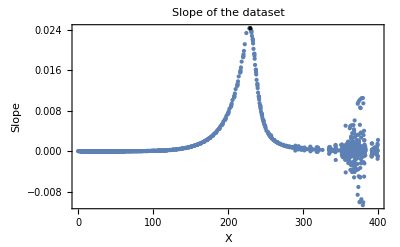

```mathematica
(*sigmadata slop plot with the peakPoint*)
ListPlot[Transpose[{Most[sigmadata[[All,1]]],slope1}],PlotStyle->PointSize[Medium],Frame->True,FrameLabel->{"X","Slope"},PlotLabel->"Slope of the dataset",Epilog->{PointSize[Large],Point[peakPoint]},PlotRange->All]
```

analyzing loop data

```mathematica
(*loopdata slop data*)
slope2 = slopes[loopdata];
{maxSlope1,maxSlopeIndex1}=MaximalBy[Transpose[{slope2,Range[Length[slope2]]}],First][[1]];
peakPoint1={loopdata[[maxSlopeIndex1]][[1]],maxSlope1};
peakPoint1[[1]]
```

228.664

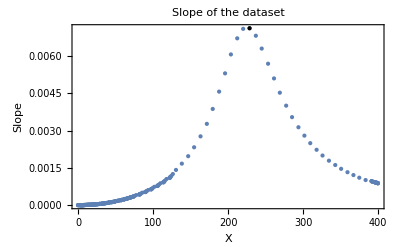

```mathematica
(*sigmadata slop plot with the peakPoint*)
ListPlot[Transpose[{Most[loopdata[[All,1]]],slope2}],PlotStyle->PointSize[Medium],Frame->True,FrameLabel->{"X","Slope"},PlotLabel->"Slope of the dataset",Epilog->{PointSize[Large],Point[peakPoint1]},PlotRange->All]
```

```mathematica
(*cretical temperature*)
Tc=(peakPoint[[1]]+peakPoint1[[1]])/2;
Tc
```

229.188